```mathematica
Clear["Global`*"]
```

# Homework #2

ASEN 5218 | Aaron Aboaf | 2020-02-18

## Question 1

### Express the linear density of the arbitrary truss made of solid cylinders where:

EE= Stiffness
ρ= Density
l_l= Length of the longeron
r_l= radius of the longeron
l_d= length of the diagonal
r_d= radius of the diagonal
θ= Angle between the diagonal and longeron
P= Global equally distributed axial load on the boom
n= number of longerons
K= some arbitrary prefactor
M/L=Linear density of the truss
R= Global truss radius

Other Notes: Boom is designed so that longerons do not Euler-buckle with the global axial load P/nand the diagonals must not buckle when experiencing a load of 1/10th of that on a longeron meaning P/(10n).

#### Moments of Inertia

```mathematica
Il=π/4 rl^4;(*longeron*)
Id=π/4 rd^4;(*diagonal*)
```

#### Local Euler Buckling

```mathematica
Pl=(n*π^2 EE*Il)/ll^2 (*longeron*)
Pd=(10n*π^2 EE*Id)/ld^2(*diagonal*)
```

(EE n π^3 rl^4)/(4 ll^2)

(5 EE n π^3 rd^4)/(2 ld^2)

#### Mass of the Truss Elements

```mathematica
Ml=π*rl^2*ρ*ll;(*longeron*)
Md=π*rd^2*ρ*ld;(*diagonal*)
```

Solve the Euler-Buckling loads for rd^2 and rl^2 so that we can substitute that into the mass equations

```mathematica
rl2=((4P*ll^2)/(n*π^3 EE))^(1/2);
rd2=((4P*ld^2)/(10*n*π^3 EE))^(1/2);
```

Substitute into Mass equations

```mathematica
Ml=π*rl2*ρ*ll
Md=π*rd2*ρ*ld
```

(2 ll √((ll^2 P)/(EE n)) ρ)/(√π)

ld √((ld^2 P)/(EE n)) √(2/(5 π)) ρ

#### Express the Length of Truss Elements in Terms of Truss Radius R and Diagonal Angle θ

Assuming that the longerons are always arranged at the vertices of a regular polygon when looking down the boom axially and that the vertices are inscribed in a circle of truss radius R then the length of a side (Ld) is given by:

```mathematica
ld=Simplify[(2R*Sin[π/n])/Cos[π/2-θ]](*diagonal*)
ll=ld*Cos[θ](*longeron*)
```

2 R Csc[θ] Sin[π/n]

2 R Cot[θ] Sin[π/n]

#### Total Mass of the Truss

The total mass of the truss is given by the addition of the mass of the diagonal and the mass of the longeron per truss unit. Since the truss is double diagonals we have 2xMd.

```mathematica
M=Ml+2Md
```

(8 R ρ Cot[θ] Sin[π/n] √((P R^2 Cot[θ]^2 Sin[π/n]^2)/(EE n)))/(√π)+8 √(2/(5 π)) R ρ Csc[θ] Sin[π/n] √((P R^2 Csc[θ]^2 Sin[π/n]^2)/(EE n))

#### Weight of the Truss

The weight of the truss is the per unit truss cell which is length l_l

```mathematica
w=M/ll
```

(Csc[π/n] ((8 R ρ Cot[θ] Sin[π/n] √((P R^2 Cot[θ]^2 Sin[π/n]^2)/(EE n)))/(√π)+8 √(2/(5 π)) R ρ Csc[θ] Sin[π/n] √((P R^2 Csc[θ]^2 Sin[π/n]^2)/(EE n))) Tan[θ])/(2 R)

Now that is super nasty so lets see if we can make it a bit nicer...

```mathematica
Together[w]
```

(4 ρ (5 Cot[θ] √((P R^2 Cot[θ]^2 Sin[π/n]^2)/(EE n))+√10 Csc[θ] √((P R^2 Csc[θ]^2 Sin[π/n]^2)/(EE n))) Tan[θ])/(5 √π)

And after some more massaging we can express the thing above as

```mathematica
K=4/(5 √π);
μR=R;
μP=√P;
μm=ρ/(√EE);
μn[n_]=Sin[π/n]/(√n);
μtheta[θ_]=Tan[θ]*(5 Cot[θ]^2+√10 Csc[θ]^2);(*(5Cot[θ]+(√10)/(Sin[θ]Cos[θ]))*)
```

```mathematica
w===K*μR*μP*μm*μn*μtheta;
```

Take the partial derivative wrt θ and n to get analytical equations for the minimum theta and minimum n

```mathematica
dn[n_]=D[μn[n],n]
```

-(π Cos[π/n])/n^(5/2)-Sin[π/n]/(2 n^(3/2))

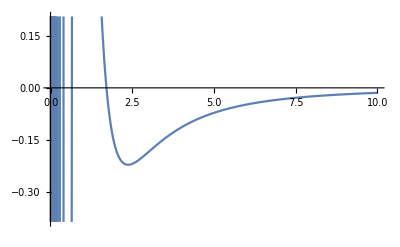

```mathematica
Plot[dn[n],{n,0,10}]
```

In the plot above we only care about the integer values because we can only have integer values of longerons and for that matter only integer values above 2 because only values of n≥2 are actually trusses. We see that there is no place where the derivative is equal to zero so there is no value of n that is optimal.

```mathematica
dtheta[θ_]=D[μtheta[θ],θ]
```

(5 Cot[θ]^2+√10 Csc[θ]^2) Sec[θ]^2+(-10 Cot[θ] Csc[θ]^2-2 √10 Cot[θ] Csc[θ]^2) Tan[θ]

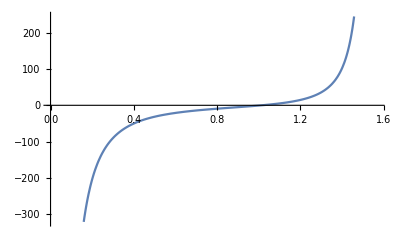

```mathematica
Plot[dtheta[θ],{θ,0,π/2}]
```

We see that there is only one value of θ between its bounds of 0 and π/2that has a derivative equal to zero. Since the transition is from negative to positive we know that it is a minimum and thus the optimal value for θ. This is approximately 58.4 degrees. We also see that this make sense because the derivative is zero (from the plot above) at the same point where MATLAB (what generated the plot below) says the minimum is.

```mathematica
-Graphics-;
```

For a given Truss Efficiency what is the maximum load as a function of the global radius?

```mathematica
Clear["Global`*"](*clear parameters for next question*)
```

## Question 2

For this question we assume the same things as Q1 except that the longerons and diagonals are made of tubes with a fixed thickness t_m. Thus the moment of inertia changes and the area equations change because we are using the rectangular area approximation for thin hollow cylinders.

#### Moments of Inertia

```mathematica
Il=π*rl^3*tm;(*longeron*)
Id=π*rd^3*tm;(*diagonal*)
```

#### Local Euler Buckling

```mathematica
Pl=(n*π^2 EE*Il)/ll^2(*longeron*)
Pd=(10n*π^2 EE*Id)/ld^2(*diagonal*)
```

(EE n π^3 rl^3 tm)/ll^2

(10 EE n π^3 rd^3 tm)/ld^2

#### Mass of the Truss Elements

```mathematica
Ml=π*rl*tm*ρ*ll;(*longeron*)
Md=π*rd*tm*ρ*ld;(*diagonal*)
```

Solve the Euler-Buckling loads for rd and rl so that we can substitute that into the mass equations

```mathematica
rl=((ll^2*P)/(EE*n*π^3*tm))^(1/3);
rd=((ld^2*P)/(EE*10n*π^3*tm))^(1/3);
```

Substitute into Mass equations

```mathematica
Ml=π*rl*ρ*ll*tm
Md=π*rd*ρ*ld*tm
```

ll ((ll^2 P)/(EE n tm))^(1/3) tm ρ

(ld ((ld^2 P)/(EE n tm))^(1/3) tm ρ)/10^(1/3)

#### Express the Length of Truss Elements in Terms of Truss Radius R and Diagonal Angle θ

Assuming that the longerons are always arranged at the vertices of a regular polygon when looking down the boom axially and that the vertices are inscribed in a circle of truss radius R then the length of a side (Ld) is given by:

```mathematica
ld=Simplify[(2R*Sin[π/n])/Cos[π/2-θ]](*diagonal*)
ll=ld*Cos[θ](*longeron*)
```

2 R Csc[θ] Sin[π/n]

2 R Cot[θ] Sin[π/n]

#### Total Mass of the Truss

The total mass of the truss is given by the addition of the mass of the diagonal and the mass of the longeron per truss unit. Since the truss is double diagonals we have 2xMd.

```mathematica
M=Ml+2Md;
```

#### Weight of the Truss

The weight of the truss is the per unit truss cell which is length l_l

```mathematica
w=M/ll
```

(Csc[π/n] (2 2^(2/3) R tm ρ Cot[θ] Sin[π/n] ((P R^2 Cot[θ]^2 Sin[π/n]^2)/(EE n tm))^(1/3)+4 (2/5)^(1/3) R tm ρ Csc[θ] Sin[π/n] ((P R^2 Csc[θ]^2 Sin[π/n]^2)/(EE n tm))^(1/3)) Tan[θ])/(2 R)

Now that is super nasty so lets see if we can make it a bit nicer...

```mathematica
Together[w]
```

1/5 tm ρ (5 2^(2/3) Cot[θ] ((P R^2 Cot[θ]^2 Sin[π/n]^2)/(EE n tm))^(1/3)+2 2^(1/3) 5^(2/3) Csc[θ] ((P R^2 Csc[θ]^2 Sin[π/n]^2)/(EE n tm))^(1/3)) Tan[θ]

And after some more massaging we can express the thing above as

```mathematica
K=1/5;
μR=R^(2/3);
μP=P^(1/3);
μm=(ρ*tm^(2/3))/EE^(1/3);
μn[n_]=Sin[π/n]^(2/3)/n^(1/3);
μtheta[θ_]=Tan[θ]*(5*2^(2/3)*Cot[θ]^(5/3)+2^(4/3)*5^(2/3)*Csc[θ]^(5/3));
```

```mathematica
w===K*μR*μP*μm*μn*μtheta
```

False

Take the partial derivative wrt θ and n to get analytical equations for the minimum theta and minimum n

```mathematica
dn[n_]=D[μn[n],n]
```

-(2 π Cos[π/n])/(3 n^(7/3) Sin[π/n]^(1/3))-Sin[π/n]^(2/3)/(3 n^(4/3))

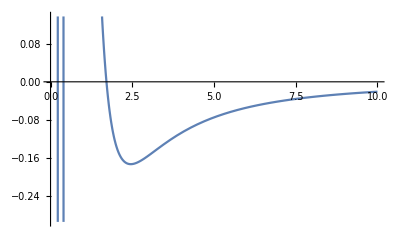

```mathematica
Plot[dn[n],{n,0,10}]
```

In the plot above we only care about the integer values because we can only have integer values of longerons and for that matter only integer values above 2 because only values of n≥2 are actually trusses. We see that there is no place where the derivative is equal to zero so there is no value of n that is optimal.

```mathematica
dtheta[θ_]=D[μtheta[θ],θ]
```

(5 2^(2/3) Cot[θ]^(5/3)+2 2^(1/3) 5^(2/3) Csc[θ]^(5/3)) Sec[θ]^2+(-25/3 2^(2/3) Cot[θ]^(2/3) Csc[θ]^2-10/3 2^(1/3) 5^(2/3) Cos[θ] Csc[θ]^(8/3)) Tan[θ]

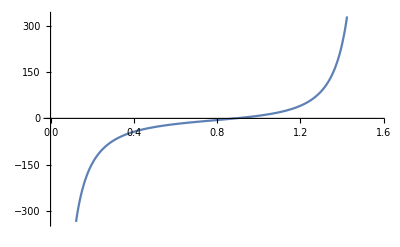

```mathematica
Plot[dtheta[θ],{θ,0,π/2}]
```

We see that there is only one value of θ between its bounds of 0 and π/2that has a derivative equal to zero. Since the transition is from negative to positive we know that it is a minimum and thus the optimal value for θ. This is approximately 68.1 degrees. Now there is something fishy here because the value of the minimum that MATLAB found was different than the place where the derivative equaled zero as calculated by Mathematica. I double and triple checked that everything matched up but there must be a bug somewhere. At this point I will just go with the MATLAB answer of 68.1 degrees.

```mathematica
-Graphics-;
```

```mathematica
Clear["Global`*"](*clear parameters for next question*)
```